#### Dimensionful 2D dynamical model for feedback

```mathematica
A1= {{ 0,λ},{-κ2, κ1}}
B1 = {{σx,0},{0,κ2*σy }}
Eigenvalues[A1]
Eigenvectors[A1]
s=Array[X,{2,2}]
s/. Expand[Solve[A1.s+s.Transpose[A1]==B1.Transpose[B1], Flatten[s]]]
```

{{0,λ},{-κ2,κ1}}

{{σx,0},{0,κ2 σy}}

{1/2 (κ1-√(κ1^2-4 κ2 λ)),1/2 (κ1+√(κ1^2-4 κ2 λ))}

{{-(-κ1-√(κ1^2-4 κ2 λ))/(2 κ2),1},{-(-κ1+√(κ1^2-4 κ2 λ))/(2 κ2),1}}

{{X[1,1],X[1,2]},{X[2,1],X[2,2]}}

{{{σx^2/(2 κ1)+(κ1 σx^2)/(2 κ2 λ)+(κ2 λ σy^2)/(2 κ1),σx^2/(2 λ)},{σx^2/(2 λ),(κ2 σx^2)/(2 κ1 λ)+(κ2^2 σy^2)/(2 κ1)}}}

#### Dimensionless feedback

```mathematica
A3= {{ 0,λt},{-κt, κt}}
B3 = {{1,0},{0,κt }}
Eigenvalues[A3]
eigens = FullSimplify[Eigenvectors[A3]]
s3=Array[Y,{2,2}]
s3/. Expand[FullSimplify[Solve[A3.s3+s3.Transpose[A3]==B3.Transpose[B3], Flatten[s3]]]]
```

{{0,λt},{-κt,κt}}

{{1,0},{0,κt}}

{1/2 (κt-√κt √(κt-4 λt)),1/2 (κt+√κt √(κt-4 λt))}

{{1/2 (1+(√(κt-4 λt))/(√κt)),1},{1/2-(√(κt-4 λt))/(2 √κt),1}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{{1/(2 κt)+1/(2 λt)+λt/2,1/(2 λt)},{1/(2 λt),κt/2+1/(2 λt)}}}

```mathematica
FullSimplify[(MatrixExp[-A3*t].{x0, y0})]
```

{ⅇ^(-(t κt)/2) (x0 Cosh[1/2 t √κt √(κt-4 λt)]+((x0 κt-2 y0 λt) Sinh[1/2 t √κt √(κt-4 λt)])/(√κt √(κt-4 λt))),ⅇ^(-(t κt)/2) (y0 Cosh[1/2 t √κt √(κt-4 λt)]+((2 x0-y0) √κt Sinh[1/2 t √κt √(κt-4 λt)])/(√(κt-4 λt)))}

```mathematica
Manipulate[Show[{ParametricPlot[%8, {t, 0, 100}, PlotRange->10], Plot[{(1/2 (1+(√(κt-4 λt))/(√κt)))^-1 x,(1/2 (1-(√(κt-4 λt))/(√κt)))^-1 x}, {x, 0, 10}, PlotStyle->Dashed]}], {λt, 0.05, 0.2}, {κt, 5, 10}, {x0, 1, 8}, {y0, 1, 8}]
```

#### Dimensionless, unamplified noise model

```mathematica
A= {{ 0,λt},{-1, 1}}
```

{{0,λt},{-1,1}}

```mathematica
X0={x0, y0}
```

{x0,y0}

```mathematica
Eigenvectors[A]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
Inverse[%3].{x0, y0};
xt0=x0/(√(1-4 λt))-y0/(√(1-4 λt));
yt0=(x0 (-1+√(1-4 λt)))/(2 √(1-4 λt))+(y0 (1+√(1-4 λt)))/(2 √(1-4 λt));
Inverse[%3].{xstar, 1};
Manipulate[Plot[{(x0/(√(1-4 λt))-y0/(√(1-4 λt)))*Exp[-1/2 (1-√(1-4 λt))t], ((x0 (-1+√(1-4 λt)))/(2 √(1-4 λt))+(y0 (1+√(1-4 λt)))/(2 √(1-4 λt)))*Exp[-1/2 (1+√(1-4 λt))t], -1/(√(1-4 λt))+(1+√(1-4 λt))/(2 √(1-4 λt)),(1+√(1-4 λt))/(2 √(1-4 λt))+((-1+√(1-4 λt)) (1+√(1-4 λt)))/(4 √(1-4 λt))},{t, 0, 100}, PlotRange->{-2, 2}], {λt, 0.01, 0.1}, {x0, 1, 2}, {y0, 1, 2}] ;
Solve[((x0 (-1+√(1-4 λt)))/(2 √(1-4 λt))+(y0 (1+√(1-4 λt)))/(2 √(1-4 λt)))*Exp[-1/2 (1+√(1-4 λt))t]==(xstar (-1+√(1-4 λt)))/(2 √(1-4 λt))+(1+√(1-4 λt))/(2 √(1-4 λt)), t];
xstarSolver [λt_, x0_, y0_]:=FindRoot[((x0-y0) ((y0+x0 (-1+√(1-4 λt))+y0 √(1-4 λt))/(1+xstar (-1+√(1-4 λt))+√(1-4 λt)))^((-1+√(1-4 λt)+2 λt)/(2 λt)))/(√(1-4 λt))==-1/(√(1-4 λt))+xstar/(√(1-4 λt)), {xstar,1}, AccuracyGoal->16][[1]];
Table[{xstarSolver[λt0, x0h, y]}, {y, y0Range}]
Transpose[{ y0Range, %164}]
```

```mathematica
MatrixExp[-A*t].X0
```

{x0 (-(ⅇ^(1/2 t (-1-√(1-4 λt))) (1-√(1-4 λt)))/(2 √(1-4 λt))+(ⅇ^(1/2 t (-1+√(1-4 λt))) (1+√(1-4 λt)))/(2 √(1-4 λt)))+y0 ((ⅇ^(1/2 t (-1-√(1-4 λt))) λt)/(√(1-4 λt))-(ⅇ^(1/2 t (-1+√(1-4 λt))) λt)/(√(1-4 λt))),x0 (-ⅇ^(1/2 t (-1-√(1-4 λt)))/(√(1-4 λt))+ⅇ^(1/2 t (-1+√(1-4 λt)))/(√(1-4 λt)))+y0 (-(ⅇ^(1/2 t (-1-√(1-4 λt))) (-1-√(1-4 λt)))/(2 √(1-4 λt))+(ⅇ^(1/2 t (-1+√(1-4 λt))) (-1+√(1-4 λt)))/(2 √(1-4 λt)))}

```mathematica
X[t_, x0_, y0_, λt_] = FullSimplify[%]
```

{ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt))),ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 λt)]+((2 x0-y0) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))}

```mathematica
Manipulate[Show[{ParametricPlot[X[t, x0, y0, λt], {t, 0, 100}, PlotRange->3], Plot[{(1/2 (1+√(1-4 λt)))^-1 x,(1/2 (1-√(1-4 λt)))^-1 x, 1}, {x, 0, 3}, PlotStyle->Dashed]}], {λt, 0.02, 0.24}, {x0, 1.5, 3}, {y0, 1.5, 3}]
```

#### Solve for the time y(t*)=1 and evaluate x(t*).

```mathematica
λs = {0.01, 0.02, 0.05, 0.1};
x0h = 1.05;
Δ=0.01;
varAndMeanFunc[λt0_, x0h_,Δ_]:=Module[{c, cf,y0h, x0Range, y0Range, params, tSolver, tvals, results, res,xpoints, grid, f},
c=2/(1+Sqrt[1-4λt0]);
cf = 2/(1+Sqrt[1-4λ]);
y0h =x0h*c;
x0Range = Table[p, {p, x0h-Δ, x0h+Δ, 0.005}];
y0Range = Table[p, {p,y0h-Δ, y0h+Δ, 0.005}];
params = Flatten[Table[{x0->x, y0->y, λt->λt0}, {x, x0Range}, {y, y0Range}], 1];
tSolver [params_]:=FindRoot[(ⅇ^(-t/2) (y0 Cosh[1/2 t √(1-4 λt)]+((2 x0-y0) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))==1)/.params, {t,(1/λt)/.params}, AccuracyGoal->16, PrecisionGoal->16][[1]];
tvals = MapThread[tSolver, {params}];
results = Transpose[{params, tvals}];
res = Table[AppendTo[r[[1]], r[[2]]], {r, results}];
xpoints =Table[ⅇ^(-t/2) (x0 Cosh[1/2 t √(1-4 λt)]+((x0-2 y0 λt) Sinh[1/2 t √(1-4 λt)])/(√(1-4 λt)))/.p, {p, res}];
grid = Flatten[Table[{x,y}, {x, x0Range}, {y, y0Range}], 1];
f = Interpolation[Transpose[{grid, xpoints}]];
Return[{f, x0h, y0h, c}];]
```

```mathematica
results=Table[varAndMeanFunc[l, x0h, Δ], {l,λs}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{InterpolatingFunction[…],1.05,1.06072,1.01021},{InterpolatingFunction[…],1.05,1.07188,1.02084},{InterpolatingFunction[…],1.05,1.10851,1.05573},{InterpolatingFunction[…],1.05,1.18337,1.12702}}

```mathematica
{f, x0h, y0h, c} = results[[1]]
```

{InterpolatingFunction[…],1.05,1.06072,1.01021}

```mathematica
Plot3D[f[x,y], {x,x0h-Δ, x0h+Δ}, {y, y0h-Δ, y0h+Δ}, AxesLabel->{"x", "y"}]
```

-Graphics3D-

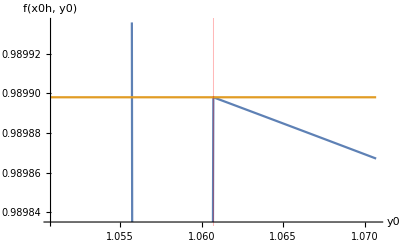

```mathematica
Show[{Plot[{f[x0h, y], 1/c},  {y, y0h-Δ, y0h+Δ}, AxesLabel->{"y0", "f(x0h, y0)"}, GridLines-> {{{y0h,Red}},None}]}]
```

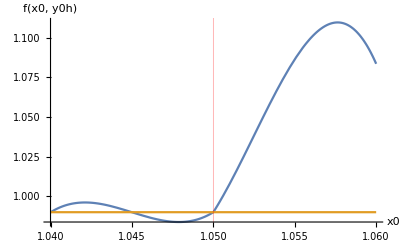

```mathematica
Plot[{f[x, y0h],1/c},  {x, x0h-Δ, x0h+Δ}, AxesLabel->{"x0", "f(x0, y0h)"}, GridLines-> {{{x0h,Red}},None}]
```

```mathematica
dFunction[f_,x0h_, y0h_, sigmaX_, sigmaY_]:=Module[{hess, fyy, fxx, fy, fx, fval},
hess = ({{D[f[x, y], {x,2}],D[f[x, y], x,y]},{D[f[x, y], x,y],D[f[x, y], {y,2}]}})/.{x->x0h, y->y0h};
fyy = hess[[2,2]];
fxx = hess[[1,1]];
fy = D[f[x, y], {y}]/.{x->x0h, y->y0h};
fx = D[f[x, y], {x}]/.{x->x0h, y->y0h};
fval = f[x, y]/.{x->x0h, y->y0h};
Return[{ sigmaY^2 fy^2,fval+sigmaY^2 fyy/2, sigmaX^2 fx^2, fval+sigmaX^2 fxx/2 }];]
```

#### width and mean with sy, lambda

```mathematica
MapThread[dFunction,{Transpose[results][[1]], Transpose[results][[2]], Transpose[results][[3]], Table[sx, 4],Table[sy, 4]}]
```

{{7.50335 sy^2,0.989898-0.00198158 sy^2,41.4332 sx^2,0.989898+1929.87 sx^2},{608.398 sy^2,0.979583+2879.41 sy^2,100.278 sx^2,0.979583+2991.84 sx^2},{103.07 sy^2,0.947214+0.303899 sy^2,0.0247948 sx^2,0.947214-2.35127 sx^2},{819.157 sy^2,0.887298+0.336663 sy^2,0.0705785 sx^2,0.887298-1.5641 sx^2}}

```mathematica
Σ[t]=FullSimplify[MatrixExp[-A*t].{{sx0, sxy0},{sxy0, sy0}}.MatrixExp[-Transpose[A]*t]];
VarDiff = FullSimplify[Σ[t][[1,1]]+Σ[t][[2,2]]-Σ[t][[1,2]]];
Σ[t][[1,1]]/.t->(2 Log[1/x0])/(-1+√(1-4 λt));
Manipulate[Plot[%27, {λt, 0.02, 0.24}, PlotRange->{-0.01, 0.1}], {x0, 1.5, 3}, {sx0, 0.1, 1}, {sy0,0.1, 1}, {sxy0, 0, 1}]
```

#### Implicit differentiation for f(x0, y0)

```mathematica
cf = 2/(1+Sqrt[1-4λ])
```

2/(1+√(1-4 λ))

```mathematica
DSolve[{y'[x]==1/λ-x/(λ *y[x])}, y[x], x, Assumptions->{1-4λ>0, λ>0, x>0, y[x]>0}]
```

Solve[-ArcTanh[(-1+(2 λ y[x])/x)/(√(1-4 λ))]/(√(1-4 λ) λ)+Log[1-y[x]/x+(λ y[x]^2)/x^2]/(2 λ)==C[1]-Log[x]/λ,y[x]]

```mathematica
FullSimplify[%, Assumptions->{x>0, y[x]>0, 1-4λ>0, λ>0}]
```

Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0,y[x]]

```mathematica
FullSimplify[Solve[2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))]+√(1-4 λ) (-2 λ C[1]+Log[x^2-x y[x]+λ y[x]^2])==0, C[1]]]
```

{{C[1]→((2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2])/(2 λ)}}

```mathematica
g[δ]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->1, x-> 1/cf + δ},  Assumptions->{1-4λ>0,λ>0}]
```

(2 ArcTanh[(1+2 δ+√(1-4 λ)-4 λ)/((1+2 δ+√(1-4 λ)) √(1-4 λ))])/(√(1-4 λ))+Log[δ (δ+√(1-4 λ))]

```mathematica
gs=FullSimplify[Series[TrigToExp[g[δ]], {δ, 0, 1}, Assumptions->δ∈Reals]]
```

(Log[δ √(1-4 λ)]-Log[-(2 δ λ)/(√(1-4 λ) (1+√(1-4 λ)-2 λ))]/(√(1-4 λ)))+(1/(1-4 λ)+1/(√(1-4 λ))) δ+O[δ]^2

```mathematica
h[x0,ϵ0]=FullSimplify[(2 ArcTanh[(x-2 λ y[x])/(x √(1-4 λ))])/(√(1-4 λ))+Log[x^2-x y[x]+λ y[x]^2]/.{y[x]->(cf*x0)+ϵ0, x->x0},Assumptions->{1-4λ>0, x0>0, λ>0}]
```

(2 ArcTanh[1-(2 ϵ0 λ)/(x0 √(1-4 λ))])/(√(1-4 λ))+Log[ϵ0 (-x0 √(1-4 λ)+ϵ0 λ)]

```mathematica
hs =FullSimplify[Series[h[x0, ϵ0], {ϵ0, 0, 1}, Assumptions->ϵ0∈Reals]]
```

(Log[-x0 ϵ0 √(1-4 λ)]-Log[(ϵ0 λ)/(x0 √(1-4 λ))]/(√(1-4 λ)))-((1+√(1-4 λ)) λ ϵ0)/(x0-4 x0 λ)+O[ϵ0]^2

```mathematica
FullSimplify[Normal@gs==Normal@hs , Assumptions->{0<λ<1/4, λ>0, x0>0, ϵ∈Reals, δ∈Reals}]
```

(1+√(1-4 λ)-4 λ) (x0 δ+ϵ0 λ)+x0 (-1+4 λ) (Log[-2 x0 δ]+√(1-4 λ) (-Log[δ]+Log[-x0 ϵ0])-Log[ϵ0 (1+√(1-4 λ)-2 λ)])==0

```mathematica
Solve[%44, δ]
```

Solve[(1+√(1-4 λ)-4 λ) (x0 δ+ϵ0 λ)+x0 (-1+4 λ) (Log[-2 x0 δ]+√(1-4 λ) (-Log[δ]+Log[-x0 ϵ0])-Log[ϵ0 (1+√(1-4 λ)-2 λ)])==0,δ]

```mathematica
%44/.δ->δ[x0, ϵ0]
```

x0 (-1+4 λ) (-Log[ϵ0 (1+√(1-4 λ)-2 λ)]+√(1-4 λ) (Log[-x0 ϵ0]-Log[δ[x0,ϵ0]])+Log[-2 x0 δ[x0,ϵ0]])+(1+√(1-4 λ)-4 λ) (ϵ0 λ+x0 δ[x0,ϵ0])==0

```mathematica
FullSimplify[D[%, ϵ0]]
```

(1+√(1-4 λ)-4 λ) (λ+x0 δ^(0,1)[x0,ϵ0])+(x0 (-1+√(1-4 λ)) (-1+4 λ) (δ[x0,ϵ0]-ϵ0 δ^(0,1)[x0,ϵ0]))/(ϵ0 δ[x0,ϵ0])==0

```mathematica
FullSimplify[Solve[%48,  Derivative[0,1][δ][x0,ϵ0]]]
```

{{δ^(0,1)[x0,ϵ0]→((ϵ0 (1+√(1-4 λ)-4 λ) λ+x0 (-1+√(1-4 λ)) (-1+4 λ)) δ[x0,ϵ0])/(x0 ϵ0 ((-1+√(1-4 λ)) (-1+4 λ)-(1+√(1-4 λ)-4 λ) δ[x0,ϵ0]))}}

```mathematica
δSolver[x0_, ϵ0_, λ_]:=FindRoot[(1+√(1-4 λ)-4 λ) (x0 δ+ϵ0 λ)+x0 (-1+4 λ) (Log[-2 x0 δ]+√(1-4 λ) (-Log[δ]+Log[-x0 ϵ0])-Log[ϵ0 (1+√(1-4 λ)-2 λ)])==0, {δ,(1*10^-3)*-Sign[ϵ0]}, AccuracyGoal->16, PrecisionGoal->16]
```

```mathematica
e0 =Range[-0.5, 0.5, 0.01]-0.0000001
```

{-0.5,-0.49,-0.48,-0.47,-0.46,-0.45,-0.44,-0.43,-0.42,-0.41,-0.4,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.3,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.0900001,-0.0800001,-0.0700001,-0.0600001,-0.0500001,-0.0400001,-0.0300001,-0.0200001,-0.0100001,-1.×10^-7,0.0099999,0.0199999,0.0299999,0.0399999,0.0499999,0.0599999,0.0699999,0.0799999,0.0899999,0.0999999,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5}

```mathematica
δNum= Table[δSolver[x0h, e, λs[[4]]], {e, e0}]
```

{{δ→0.0213669+0. ⅈ},{δ→0.0210198+0. ⅈ},{δ→0.0206692+0. ⅈ},{δ→0.0203153+0. ⅈ},{δ→0.019958+0. ⅈ},{δ→0.0195974+0. ⅈ},{δ→0.0192333+0. ⅈ},{δ→0.018866+0. ⅈ},{δ→0.0184952+0. ⅈ},{δ→0.0181211+0. ⅈ},{δ→0.0177437+0. ⅈ},{δ→0.017363+0. ⅈ},{δ→0.0169789+0. ⅈ},{δ→0.0165914+0. ⅈ},{δ→0.0162007+0. ⅈ},{δ→0.0158067+0. ⅈ},{δ→0.0154093+0. ⅈ},{δ→0.0150087+0. ⅈ},{δ→0.0146047+0. ⅈ},{δ→0.0141975+0. ⅈ},{δ→0.013787+0. ⅈ},{δ→0.0133733+0. ⅈ},{δ→0.0129563+0. ⅈ},{δ→0.012536+0. ⅈ},{δ→0.0121125+0. ⅈ},{δ→0.0116858+0. ⅈ},{δ→0.0112559+0. ⅈ},{δ→0.0108227+0. ⅈ},{δ→0.0103864+0. ⅈ},{δ→0.00994688+0. ⅈ},{δ→0.00950418+0. ⅈ},{δ→0.00905831+0. ⅈ},{δ→0.00860928+0. ⅈ},{δ→0.0081571+0. ⅈ},{δ→0.00770179+0. ⅈ},{δ→0.00724336+0. ⅈ},{δ→0.00678181+0. ⅈ},{δ→0.00631716+0. ⅈ},{δ→0.00584943+0. ⅈ},{δ→0.00537861+0. ⅈ},{δ→0.00490473+0. ⅈ},{δ→0.0044278+0. ⅈ},{δ→0.00394782+0. ⅈ},{δ→0.00346481+0. ⅈ},{δ→0.00297879+0. ⅈ},{δ→0.00248976+0. ⅈ},{δ→0.00199774+0. ⅈ},{δ→0.00150274+0. ⅈ},{δ→0.00100478+0. ⅈ},{δ→0.000503862+0. ⅈ},{δ→5.05323×10^-9+0. ⅈ},{δ→-0.000506779+0. ⅈ},{δ→-0.00101648+0. ⅈ},{δ→-0.00152907+0. ⅈ},{δ→-0.00204456+0. ⅈ},{δ→-0.00256291+0. ⅈ},{δ→-0.00308413+0. ⅈ},{δ→-0.00360819+0. ⅈ},{δ→-0.00413509+0. ⅈ},{δ→-0.0046648+0. ⅈ},{δ→-0.00519731+0. ⅈ},{δ→-0.00573262+0. ⅈ},{δ→-0.0062707+0. ⅈ},{δ→-0.00681154+0. ⅈ},{δ→-0.00735513+0. ⅈ},{δ→-0.00790146+0. ⅈ},{δ→-0.0084505+0. ⅈ},{δ→-0.00900225+0. ⅈ},{δ→-0.00955669+0. ⅈ},{δ→-0.0101138+0. ⅈ},{δ→-0.0106736+0. ⅈ},{δ→-0.011236+0. ⅈ},{δ→-0.0118011+0. ⅈ},{δ→-0.0123687+0. ⅈ},{δ→-0.012939+0. ⅈ},{δ→-0.0135119+0. ⅈ},{δ→-0.0140873+0. ⅈ},{δ→-0.0146653+0. ⅈ},{δ→-0.0152459+0. ⅈ},{δ→-0.015829+0. ⅈ},{δ→-0.0164146+0. ⅈ},{δ→-0.0170027+0. ⅈ},{δ→-0.0175933+0. ⅈ},{δ→-0.0181863+0. ⅈ},{δ→-0.0187819+0. ⅈ},{δ→-0.0193798+0. ⅈ},{δ→-0.0199802+0. ⅈ},{δ→-0.020583+0. ⅈ},{δ→-0.0211882+0. ⅈ},{δ→-0.0217958+0. ⅈ},{δ→-0.0224058+0. ⅈ},{δ→-0.0230181+0. ⅈ},{δ→-0.0236328+0. ⅈ},{δ→-0.0242498+0. ⅈ},{δ→-0.0248691+0. ⅈ},{δ→-0.0254907+0. ⅈ},{δ→-0.0261146+0. ⅈ},{δ→-0.0267408+0. ⅈ},{δ→-0.0273692+0. ⅈ},{δ→-0.0279999+0. ⅈ},{δ→-0.0286328+0. ⅈ}}

```mathematica
Re[δ/.%]
```

{0.0213669,0.0210198,0.0206692,0.0203153,0.019958,0.0195974,0.0192333,0.018866,0.0184952,0.0181211,0.0177437,0.017363,0.0169789,0.0165914,0.0162007,0.0158067,0.0154093,0.0150087,0.0146047,0.0141975,0.013787,0.0133733,0.0129563,0.012536,0.0121125,0.0116858,0.0112559,0.0108227,0.0103864,0.00994688,0.00950418,0.00905831,0.00860928,0.0081571,0.00770179,0.00724336,0.00678181,0.00631716,0.00584943,0.00537861,0.00490473,0.0044278,0.00394782,0.00346481,0.00297879,0.00248976,0.00199774,0.00150274,0.00100478,0.000503862,5.05323×10^-9,-0.000506779,-0.00101648,-0.00152907,-0.00204456,-0.00256291,-0.00308413,-0.00360819,-0.00413509,-0.0046648,-0.00519731,-0.00573262,-0.0062707,-0.00681154,-0.00735513,-0.00790146,-0.0084505,-0.00900225,-0.00955669,-0.0101138,-0.0106736,-0.011236,-0.0118011,-0.0123687,-0.012939,-0.0135119,-0.0140873,-0.0146653,-0.0152459,-0.015829,-0.0164146,-0.0170027,-0.0175933,-0.0181863,-0.0187819,-0.0193798,-0.0199802,-0.020583,-0.0211882,-0.0217958,-0.0224058,-0.0230181,-0.0236328,-0.0242498,-0.0248691,-0.0254907,-0.0261146,-0.0267408,-0.0273692,-0.0279999,-0.0286328}

```mathematica
Transpose[{y0h+e0, %+1/c}]
```

{{2.26393,0.744974},{2.27393,0.744627},{2.28393,0.744276},{2.29393,0.743922},{2.30393,0.743565},{2.31393,0.743204},{2.32393,0.74284},{2.33393,0.742473},{2.34393,0.742102},{2.35393,0.741728},{2.36393,0.741351},{2.37393,0.74097},{2.38393,0.740586},{2.39393,0.740198},{2.40393,0.739807},{2.41393,0.739413},{2.42393,0.739016},{2.43393,0.738615},{2.44393,0.738212},{2.45393,0.737804},{2.46393,0.737394},{2.47393,0.73698},{2.48393,0.736563},{2.49393,0.736143},{2.50393,0.735719},{2.51393,0.735293},{2.52393,0.734863},{2.53393,0.73443},{2.54393,0.733993},{2.55393,0.733554},{2.56393,0.733111},{2.57393,0.732665},{2.58393,0.732216},{2.59393,0.731764},{2.60393,0.731309},{2.61393,0.73085},{2.62393,0.730389},{2.63393,0.729924},{2.64393,0.729456},{2.65393,0.728985},{2.66393,0.728512},{2.67393,0.728035},{2.68393,0.727555},{2.69393,0.727072},{2.70393,0.726586},{2.71393,0.726097},{2.72393,0.725605},{2.73393,0.72511},{2.74393,0.724612},{2.75393,0.724111},{2.76393,0.723607},{2.77393,0.7231},{2.78393,0.72259},{2.79393,0.722078},{2.80393,0.721562},{2.81393,0.721044},{2.82393,0.720523},{2.83393,0.719999},{2.84393,0.719472},{2.85393,0.718942},{2.86393,0.718409},{2.87393,0.717874},{2.88393,0.717336},{2.89393,0.716795},{2.90393,0.716252},{2.91393,0.715705},{2.92393,0.715156},{2.93393,0.714605},{2.94393,0.71405},{2.95393,0.713493},{2.96393,0.712933},{2.97393,0.712371},{2.98393,0.711806},{2.99393,0.711238},{3.00393,0.710668},{3.01393,0.710095},{3.02393,0.709519},{3.03393,0.708941},{3.04393,0.708361},{3.05393,0.707778},{3.06393,0.707192},{3.07393,0.706604},{3.08393,0.706014},{3.09393,0.70542},{3.10393,0.704825},{3.11393,0.704227},{3.12393,0.703627},{3.13393,0.703024},{3.14393,0.702419},{3.15393,0.701811},{3.16393,0.701201},{3.17393,0.700589},{3.18393,0.699974},{3.19393,0.699357},{3.20393,0.698738},{3.21393,0.698116},{3.22393,0.697492},{3.23393,0.696866},{3.24393,0.696238},{3.25393,0.695607},{3.26393,0.694974}}

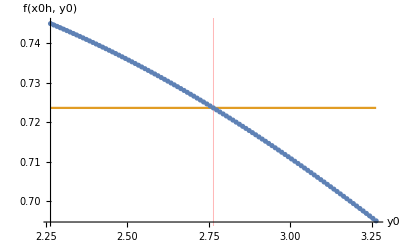

```mathematica
Show[{Plot[{f[x0h, y], 1/c},  {y, y0h-0.5, y0h+0.5}, AxesLabel->{"y0", "f(x0h, y0)"}, GridLines-> {{{y0h,Red}},None}], ListPlot[%64]}]
```

```mathematica
(1+√(1-4 λ)-4 λ) (x0 δ+ϵ0 λ)+x0 (-1+4 λ) (Log[-2 x0 δ]+√(1-4 λ) (-Log[δ]+Log[-x0 ϵ0])-Log[ϵ0 (1+√(1-4 λ)-2 λ)])/.δ->-m*ϵ0
```

(1+√(1-4 λ)-4 λ) (-m x0 ϵ0+ϵ0 λ)+x0 (-1+4 λ) (√(1-4 λ) (-Log[-m ϵ0]+Log[-x0 ϵ0])+Log[2 m x0 ϵ0]-Log[ϵ0 (1+√(1-4 λ)-2 λ)])

```mathematica
FullSimplify[x0 (-1+4 λ) (√(1-4 λ) (-Log[-m ϵ0]+Log[-x0 ϵ0])+Log[2 m x0 ϵ0]-Log[ϵ0 (1+√(1-4 λ)-2 λ)])]
```

x0 (-1+4 λ) (√(1-4 λ) (-Log[-m ϵ0]+Log[-x0 ϵ0])+Log[2 m x0 ϵ0]-Log[ϵ0 (1+√(1-4 λ)-2 λ)])

```mathematica
Solve[%==0, m]
```

$Aborted

```mathematica
Exp[ (√(1-4 λ) (-Log[-m ϵ0]+Log[-x0 ϵ0])+Log[2 m x0 ϵ0]-Log[ϵ0 (1+√(1-4 λ)-2 λ)])]
```

(2 ⅇ^(√(1-4 λ) (-Log[-m ϵ0]+Log[-x0 ϵ0])) m x0)/(1+√(1-4 λ)-2 λ)

```mathematica
FullSimplify[(2*m*x0/(1+√(1-4 λ)-2 λ))(x0/m)^(√(1-4 λ)), Assumptions->{m>0, x0>0, 1/4>λ>0}]
```

(2 m x0 (x0/m)^(√(1-4 λ)))/(1+√(1-4 λ)-2 λ)

```mathematica
Solve[%==1, m]
```

Solve[(2 m x0 (x0/m)^(√(1-4 λ)))/(1+√(1-4 λ)-2 λ)==1,m]

```mathematica
((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))/.{x0->2, λ->0.20}
```

0.0505323

```mathematica
%^2
```

0.00255351

```mathematica
((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))/.{x0->1.05, λ->0.01}
```

0.00307017

```mathematica
((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))/.{x0->1.05, λ->0.02}
```

0.0350402

```mathematica
%^2
```

0.00122781

```mathematica
fpFunc[λ_, x0_]:=((1+Sqrt[1-4λ]-2λ)/(2*x0^(1+Sqrt[1-4λ])))^(1/(1-Sqrt[1-4λ]))
```

```mathematica
fpFunc[0.05, 1.05]^2
```

0.022243